```mathematica
SetDirectory[NotebookDirectory[]];
CvData = Import["64_cv.dat","Table"];
MagnetData = Import["64_magnetization.dat","Table"];
SusceptData = Import["64_susceptibility.dat","Table"];
```

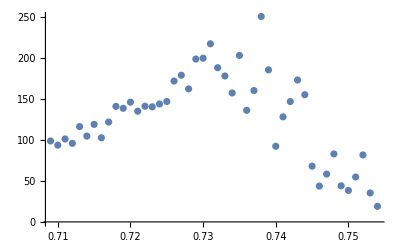

```mathematica
ListPlot[Take[SusceptData,{410, 455}], PlotRange->Full]
```

```mathematica
SusceptFit = NonlinearModelFit[Take[SusceptData,{410,455}],A*Exp[-( x-mu)^2/(2 Sigma^2)],{{A,170},Sigma,mu},x];
```

```mathematica
SusceptFit[{"BestFit","ParameterTable"}]
```

{185.373 ⅇ^(-2431.6 (-0.729533+x)^2), | Estimate | Standard Error | t-Statistic | P-Value
A | 185.373 | 7.56282 | 24.5111 | 6.73782×10^-27
Sigma | 0.0143397 | 0.000868273 | 16.5151 | 3.138×10^-20
mu | 0.729533 | 0.000701016 | 1040.68 | 2.86584×10^-96}

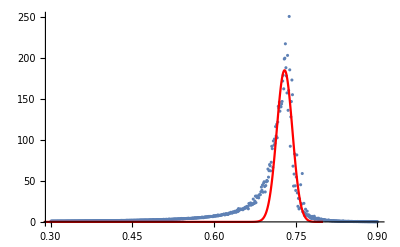

```mathematica
Show[ListPlot[SusceptData, PlotRange->Full],Plot[SusceptFit[x],{x,0,0.8},PlotRange->{{0,0.8},{0,500}}, PlotStyle->Red]]
```

```mathematica
a
```

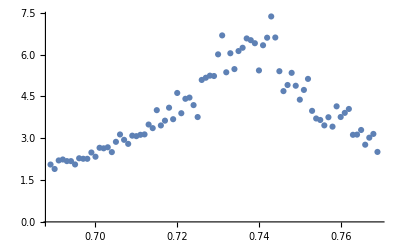

```mathematica
ListPlot[Take[CvData,{390,470}]]
```

```mathematica
CvFit = NonlinearModelFit[Take[CvData,{390,470}],A*Exp[-( x-mu)^2/(2*Sigma^2)],{{A,3.6},Sigma,mu},x]
```

FittedModel[5.62878 ⅇ^(-697.659 (-«19»+x)^2)]

```mathematica
CvFit[{"BestFit","ParameterTable"}]
```

{5.62878 ⅇ^(-697.659 (-0.736593+x)^2), | Estimate | Standard Error | t-Statistic | P-Value
A | 5.62878 | 0.115183 | 48.8681 | 2.9151×10^-60
Sigma | -0.0267709 | 0.000890377 | -30.067 | 1.17752×10^-44
mu | 0.736593 | 0.000707228 | 1041.52 | 2.32741×10^-163}

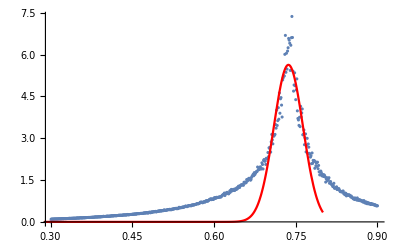

```mathematica
Show[ListPlot[CvData, PlotRange->Full],Plot[CvFit[x],{x,0,0.8},PlotRange->Full,PlotStyle->Red]]
```